# DrawPauliStringAsTree

```mathematica
SetDirectory @ NotebookDirectory[];
Import["../Link/QuESTlink.m"];
```

## Doc

```mathematica
?DrawPauliStringAsTree
```

## Correctness

## Pauli strings

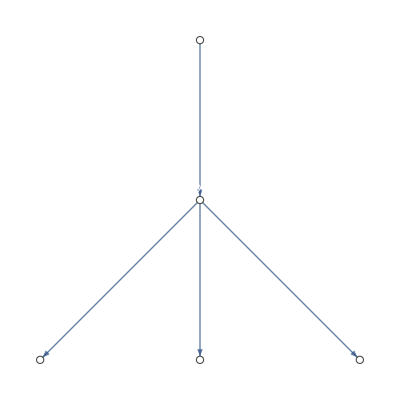

```mathematica
DrawPauliStringAsTree[Subscript[X, 1] Subscript[X, 0]+Subscript[X, 1] Subscript[Y, 0]+Subscript[X, 1] Subscript[Z, 0]]
```

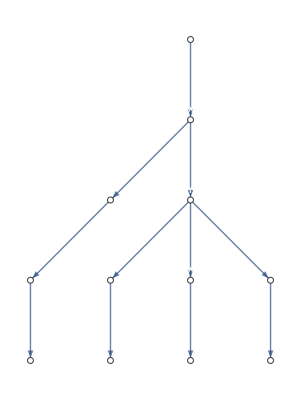

```mathematica
DrawPauliStringAsTree @ SimplifyPaulis[ Subscript[Y, 2] Subscript[X, 3](Subscript[X, 0]+Subscript[Y, 0] Subscript[Z, 1]+Subscript[X, 1] Subscript[Z, 0]) + Subscript[X, 3] Subscript[X, 0]]
```

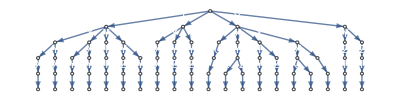

```mathematica
DrawPauliStringAsTree @ GetRandomPauliString[5,20]
```

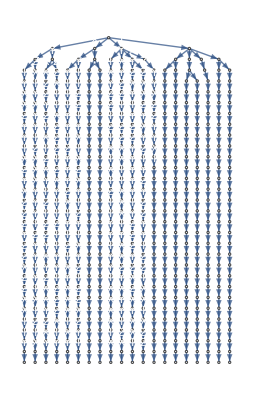

```mathematica
DrawPauliStringAsTree @ GetRandomPauliString[30,20]
```

## “SmallestIsRoot” -> True

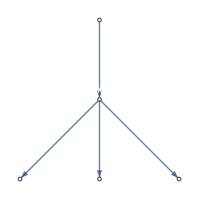

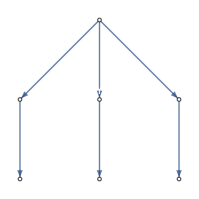

```mathematica
DrawPauliStringAsTree[Subscript[X, 1] Subscript[X, 0]+Subscript[X, 1] Subscript[Y, 0]+Subscript[X, 1] Subscript[Z, 0], "SmallestIsRoot"->False]
DrawPauliStringAsTree[Subscript[X, 1] Subscript[X, 0]+Subscript[X, 1] Subscript[Y, 0]+Subscript[X, 1] Subscript[Z, 0], "SmallestIsRoot"->True]
```

## Graph options

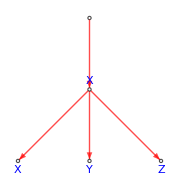

```mathematica
DrawPauliStringAsTree[
	Subscript[X, 1] Subscript[X, 0]+Subscript[X, 1] Subscript[Y, 0]+Subscript[X, 1] Subscript[Z, 0], 
	EdgeStyle->Red,
	VertexLabelStyle->Blue
]
```

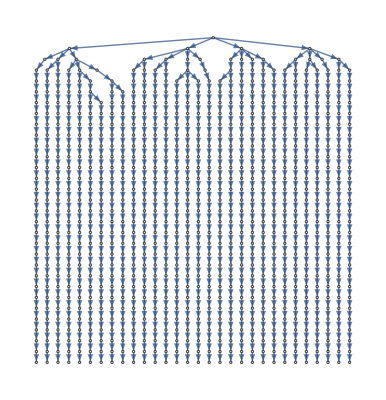

```mathematica
DrawPauliStringAsTree[
	GetRandomPauliString[30,30],
	VertexLabels->None
]
```

## Errors

```mathematica
DrawPauliStringAsTree[]
```

DrawPauliStringAsTree::error: Invalid arguments. See ?DrawPauliStringAsTree

$Failed

```mathematica
DrawPauliStringAsTree[Subscript[X, 0]-1]
```

DrawPauliStringAsTree::error: Invalid arguments. See ?DrawPauliStringAsTree

$Failed

```mathematica
(* still permit drawing on bad option *)
DrawPauliStringAsTree[Subscript[X, 1] Subscript[X, 0]+Subscript[X, 1] Subscript[Z, 0], badopt->True]
```

OptionValue::nodef: Unknown option badopt for {DrawPauliStringAsTree,Graph}.

-Graphics-